```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

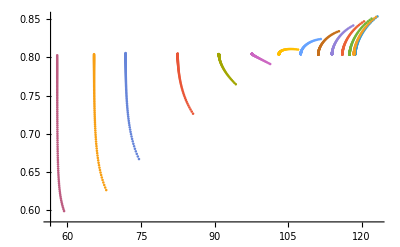

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.01,{x,fitdata[[i]][[90]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p01.dat",%];
```

FindRoot::reged: 点 {118.72} 位于搜索区域 {118.72,123.231} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {118.431} 位于搜索区域 {118.431,122.931} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {117.557} 位于搜索区域 {117.557,122.024} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{118.72,118.431,117.557,116.079,113.963,111.156,107.581,103.465,101.184,90.8833,82.4833,71.8598,65.4291,57.9168}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.02,{x,fitdata[[i]][[90]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p02.dat",%];
```

FindRoot::reged: 点 {118.72} 位于搜索区域 {118.72,123.231} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {118.431} 位于搜索区域 {118.431,122.931} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {117.557} 位于搜索区域 {117.557,122.024} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

InterpolatingFunction::dmval: 输入值 {101.353} 位于插值函数的数据范围之外. 将使用外推法.

{118.72,118.431,117.557,116.079,113.963,111.717,108.562,105.566,101.353,91.943,82.4833,71.8598,65.4291,57.9168}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.8)/0.8]==0.03,{x,fitdata[[i]][[90]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p03.dat",%];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

InterpolatingFunction::dmval: 输入值 {101.353} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {101.353} 位于搜索区域 {97.643,101.353} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {82.4833} 位于搜索区域 {82.4833,85.6177} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {71.8598} 位于搜索区域 {71.8598,74.5905} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{119.516,119.24,118.409,117.02,115.081,112.699,111.413,105.566,101.353,92.7911,82.4833,71.8598,65.4291,57.9168}

```mathematica
Export["mub.dat",mub]
```

mub.dat

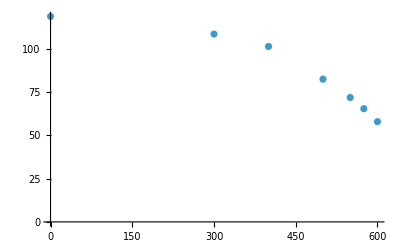

```mathematica
ListPlot[Transpose[{mub,T}],PlotRange->All]
```